```mathematica
(*μRo=1;
Binit=20;
B=1/(2Binit);
σRo=Sqrt[B]//N
(*σRo=0.1;*)
RoPDF=NormalDistribution[μRo,σRo];
momRo[i_]:=Moment[RoPDF,i];
nro=5;
momRos=Table[momRo[i],{i,0,2nro-1}];
{Ros,wRos}=orthog[momRos,nro]
B=(σRo)^2 2 Binit^2*)
```

```mathematica
ClearAll["Global`*"];

γ=1.4;
Nperiod=30;
T=Nperiod 3.4 pratio^0.75;
pratio=0.8;

Nt=100;
ts=Table[i,{i,T/Nt,T,T/Nt}];
Nt=Length[ts];

μRo=0;
σRo=0.2;
RoPDF=LogNormalDistribution[μRo,σRo];
momRo[i_]:=Moment[RoPDF,i];
f[x_]:=PDF[RoPDF,x];

Rey=10 10^6;
Rey=Infinity;
Ca=1;
c=1;
β[x_]:=2/(Rey x^2);
ω2[x_]:=(3 γ Ca)/x^2;
myr0[x_,t_]:=x Exp[-β[x] t]Cos[t Sqrt[ω2[x]-β[x]^2]];
mydr0=D[myr0[x,t],t];

pow[x_,0]:=1/;x==0||x==0.
pow[x_,y_:0]:=x^y

moms={{1,0}};

(* Gaussian-Hermite quadrature points *)
RosF=Import["/Users/spencerbryngelson/Documents/Caltech/Research/analysis/qbmm/D/quadpts/x_*.dat"];
wRosF=Import["/Users/spencerbryngelson/Documents/Caltech/Research/analysis/qbmm/D/quadpts/w_*.dat"];
ns=Table[i,{i,1,Length[RosF],2}];
nros=Table[Length[RosF[[i]]],{i,ns}];

(* Simpson's rule stuff *)
R0min=0.1;
R0max=10.0;
k=1;
Do[
RosS[i]={};wRosS[i]={};phi={};
nro=nros[[k]];
Do[
AppendTo[phi,Log[R0min]+((ir-1)Log[R0max/R0min])/(nro-1)];
AppendTo[RosS[i],Exp[phi[[ir]]]];
,{ir,1,nro}];
dphi=phi[[2]]-phi[[1]];

Do[
tmp=1/(2 Pi σRo)Exp[-1/2(phi[[ir]]/σRo)^2];
If[EvenQ[ir],
AppendTo[wRosS[i],tmp 4/3 dphi],
AppendTo[wRosS[i],tmp 2/3 dphi]
];
,{ir,2,nro-1}];
tmp=1/(2 Pi σRo)Exp[-1/2(phi[[1]]/σRo)^2];
PrependTo[wRosS[i],tmp dphi/3.];
tmp=1/(2 Pi σRo)Exp[-1/2(phi[[nro]]/σRo)^2];
AppendTo[wRosS[i],tmp dphi/3.];
k=k+1;
,{i,ns}];
```

```mathematica
Do[
(*nros[[l]];*)
(*momRos=Table[momRo[i],{i,0,2nro-1}];
{Ros,wRos}=orthog[momRos,nro];*)
Ros=Flatten[RosF[[l]]];
wRos=Flatten[wRosF[[l]]];
nro=Length[Ros];
Print[nro(*,"  1"*)];

(* Rayleigh-Plesset *)
myr=ParallelTable[r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 == (Ros[[i]]/r[t])^(3γ)-1/pratio,r[0]==Ros[[i]],r'[0]==0},
r[t],
{t,0,T}]//First//First);
,{i,1,nro}];

(* Keller-Miksis *)
(*myr=ParallelTable[r[t]/.(NDSolve[
{(1-r'[t]/c)r[t]r''[t]+3/2 r'[t]^2(1-r'[t]/(3 c)) == (1+r'[t]/c)((Ros[[i]]/r[t])^(3γ)-1/pratio),r[0]==Ros[[i]],r'[0]==0},
r[t],
{t,0,T}]//First//First)
,{i,1,nro}];*)
mydr=Table[D[myr[[i]],t],{i,1,nro}];

(*Do[momev[k,l]=Table[Sum[wRos[[i]]pow[myr[[i]]/.{t->ts[[j]]},moms[[k,1]]]pow[mydr[[i]]/.{t->ts[[j]]},moms[[k,2]]],{i,1,nro}],{j,1,Nt}];
,{k,1,Length[moms]}];*)

(* Linear *)
(* Gaussian quadrature *)
(*Do[
R=Ros[[i]];
myr[i]=myr0[R,t];
mydr[i]=mydr0/.{x->R};
,{i,1,nro}];*)

Do[momev[k,l]=
Table[
Sum[
wRos[[i]]pow[myr[i]/.{t->ts[[j]]},moms[[k,1]]]pow[mydr[i]/.{t->ts[[j]]},moms[[k,2]]]
,{i,1,nro}]
,{j,1,Nt}];
,{k,1,Length[moms]}];

(* Simpson's rule *)
Do[
R=RosS[l][[i]];
myr[i]=myr0[R,t];
mydr[i]=mydr0/.{x->R};
,{i,1,nro}];

Do[momevS[k,l]=
Table[
Sum[
wRosS[l][[i]]pow[myr[i]/.{t->ts[[j]]},moms[[k,1]]]pow[mydr[i]/.{t->ts[[j]]},moms[[k,2]]]
,{i,1,nro}]
,{j,1,Nt}];
,{k,1,Length[moms]}];

,{l,ns}];
```

11

31

51

71

91

111

131

151

171

191

```mathematica
exact[i_,j_,t_]:=NIntegrate[
f[x]myr0[x,t]^i mydr0^j,{x,10^-20,10},
MinRecursion->9,AccuracyGoal->10,WorkingPrecision->15];
Do[exacts[j]=Table[exact[moms[[j,1]],moms[[j,2]],ts[[k]]],{k,1,Nt}];
,{j,1,Length[moms]}];

(*Do[err[j,i]=Abs[momev[j,i]-momev[j,Last[ns]]]
,{i,Drop[ns,-1]},{j,1,Length[moms]}];*)
Do[errG[j,i]=Abs[momev[j,i]-exacts[j]]
,{i,ns},{j,1,Length[moms]}];
Do[errS[j,i]=Abs[momevS[j,i]-exacts[j]]
,{i,ns},{j,1,Length[moms]}];
```

```mathematica
Table[LogLinearPlot[f[x]myr0[x,t]/.{t->ts[[i]]},{x,0.1,3},PlotRange->All,PlotLabel->ts[[i]]],{i,1,Nt,Floor[Nt/10.]}]
```

$Aborted

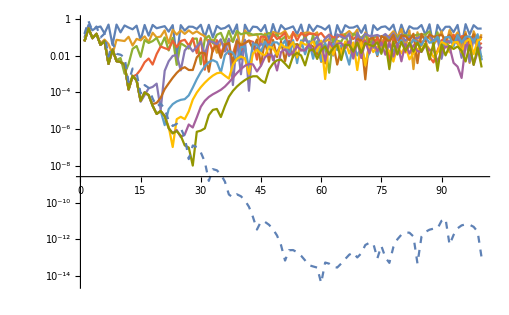

```mathematica
Show[
ListLogPlot[Abs[Table[momevS[1,i],{i,ns}]],Joined->True,PlotRange->All],
ListLogPlot[Abs[exacts[1]],Joined->True,PlotRange->All,PlotStyle->Dashed],PlotRange->All
]
```

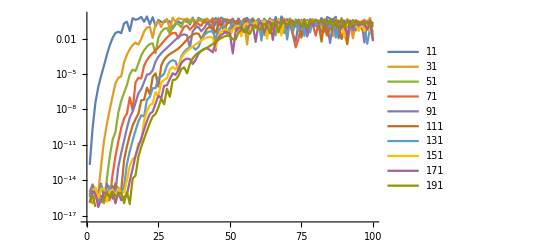

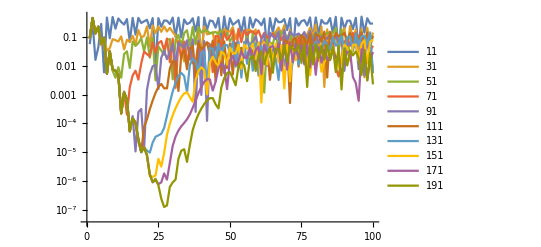

```mathematica
ListLogPlot[Table[errG[1,i],{i,ns}],Joined->True,PlotLegends->nros]
ListLogPlot[Table[errS[1,i],{i,ns}],Joined->True,PlotLegends->nros]
```

```mathematica
Ro=0.0002;
sol=r[t]/.(NDSolve[
{r[t] r''[t]+3/2 r'[t]^2 == (Ro/r[t])^(3γ)-1/pratio,r[0]==Ro,r'[0]==0},
r[t],
{t,0,T}]//First//First);
```

```mathematica
int=f[x]myr0[x,10]^2;
NIntegrate[
int,{x,10^-4,10},Method->{"LevinRule","Points"->30,"MethodSwitching"->False},MaxRecursion->0,AccuracyGoal->10,WorkingPrecision->10]
exact=NIntegrate[
int,{x,10^-4,10},MinRecursion->9,AccuracyGoal->10,WorkingPrecision->10]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 0 recursive bisections in x near {x} = {10.}. NIntegrate obtained 3.20999504×10^-8 and 3.20999504×10^-8 for the integral and error estimates.

3.20999504×10^-8

0.5416421125

```mathematica
myr0[x,t]//N
```

2.71828^(-(2.×10^-7 t)/x^2) x Cos[t √(-(4.×10^-14)/x^4+4.2/x^2)]

```mathematica
li=NIntegrate`LevinIntegrandReduce[f[x] myr0[x,t]//N(*x Exp[I x] BesselJ[0,100 x]+Sqrt[x]*),x]
li["Rules"]
```

NIntegrate`LevinIntegrand[2,ⅇ^(-(2.×10^-7 t)/x^2) x Cos[t √(-(4.×10^-14)/x^4+4.2/x^2)] (Piecewise[{{(1.99471 2.71828^(-12.5 Log[x]^2))/x, x>0.}, {0., True}}]),{x},<>]

{Variables→{x},AdditiveTerm→0,Amplitude→{x (Piecewise[{{(1.99471 2.71828^(-12.5 Log[x]^2))/x, x>0.}, {0., True}}]),0},Kernel→{ⅇ^(-(2.×10^-7 t)/x^2) Cos[t √(-(4.×10^-14)/x^4+4.2/x^2)],-ⅇ^(-(2.×10^-7 t)/x^2) Sin[t √(-(4.×10^-14)/x^4+4.2/x^2)]},DifferentialMatrices→{{{(4.×10^-7 t)/x^3,(t ((1.6×10^-13)/x^5-8.4/x^3))/(2 √(-(4.×10^-14)/x^4+4.2/x^2))},{-(t ((1.6×10^-13)/x^5-8.4/x^3))/(2 √(-(4.×10^-14)/x^4+4.2/x^2)),(4.×10^-7 t)/x^3}}}}

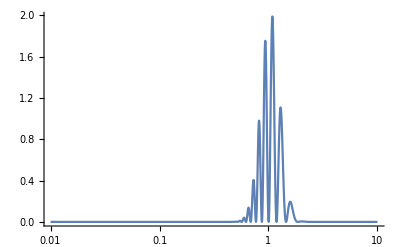

```mathematica
LogLinearPlot[int,{x,0.01,10},PlotRange->All]
```

```mathematica
myr0[x_,t_]:=x Exp[-β[x] t]Cos[t Sqrt[ω2[x]-β[x]^2]];
```

```mathematica
myr0[x,10]
```

x Cos[20.4939 √(1/x^2)]

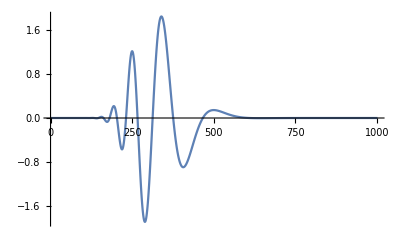

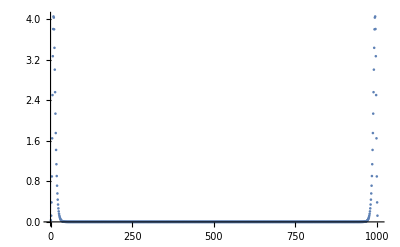

```mathematica
b=3;
a=0.1;
n=1000;
t=10;
ic=Table[f[x]myr0[x,t],{x,a,b,(b-a)/n}];
ListPlot[ic,Joined->True,PlotRange->All]
ListPlot[Abs[Fourier[ic]],PlotRange->All]
```

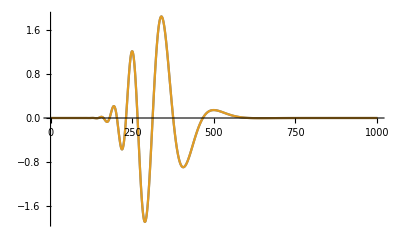

```mathematica
ListPlot[{Re[InverseFourier[Fourier[ic]]],ic},Joined->True,PlotRange->All]
```

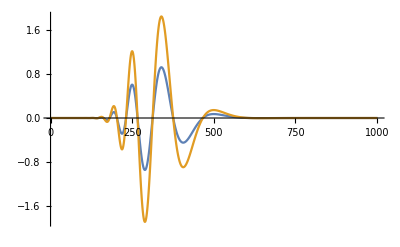

```mathematica
keep=Length[fourier]-100;
fourier=Fourier[ic,FourierParameters->{-1,1}];
inv=InverseFourier[PadRight[Take[fourier,keep],Length[fourier]],FourierParameters->{-1,1}];
ListPlot[{Re[inv],ic},Joined->True,PlotRange->All]
```